# EOH FD basis

#### Create the Hamiltonian in the finite difference basis,

```mathematica
Xfd:=SparseArray[{i_,i_}->(2i-9)/2 ,{8,8}]
s=SparseArray[{{i_,i_}->1,{i_,j_}/;i-j==-1->-1},{8,8}]
P2:= s+Transpose[s]
HamiltonianFdEOHSHO :=N[ 1/2(√(8/2))(√(8/2))P2+ 1/2  MatrixPower[Xfd/(√(8/2)),2] 
]
Reverse[N[Eigenvalues[HamiltonianFdEOHSHO]]]
```

SparseArray[…]

{0.506987,1.56896,2.76327,4.10056,5.48512,6.75293,7.86962,8.20256}

#### Save the Hamiltonian,

```mathematica
SetDirectory[NotebookDirectory[]];
saveHam[ham_]:=Export["./"<>"Hamfdbh.txt",ham,"Table"]
saveHam[HamiltonianFdEOHSHO];
```

#### Classical computations of the EOH

```mathematica
MatrixExp[-ⅈ t  HamiltonianFdEOHSHO][[1,1]]
```

(0.0319198-0.0861342 ⅈ) ((0.+0. ⅈ)+(0.0319198+0.0861342 ⅈ) (ⅇ^(2.22045×10^-16 t) Cos[0.506987 t]-ⅈ ⅇ^(2.22045×10^-16 t) Sin[0.506987 t]))+(0.188134-0.107642 ⅈ) ((0.+0. ⅈ)+(0.188134+0.107642 ⅈ) (ⅇ^(1.28023×10^-15 t) Cos[1.56896 t]-ⅈ ⅇ^(1.28023×10^-15 t) Sin[1.56896 t]))+(0.134856-0.315563 ⅈ) ((0.+0. ⅈ)+(0.134856+0.315563 ⅈ) (ⅇ^(8.68663×10^-16 t) Cos[2.76327 t]-ⅈ ⅇ^(8.68663×10^-16 t) Sin[2.76327 t]))+(0.208796-0.376444 ⅈ) ((0.+0. ⅈ)+(0.208796+0.376444 ⅈ) (ⅇ^(-8.68229×10^-16 t) Cos[4.10056 t]-ⅈ ⅇ^(-8.68229×10^-16 t) Sin[4.10056 t]))-(0.359107-0.288308 ⅈ) ((0.+0. ⅈ)-(0.359107+0.288308 ⅈ) (ⅇ^(-4.44566×10^-15 t) Cos[5.48512 t]-ⅈ ⅇ^(-4.44566×10^-15 t) Sin[5.48512 t]))+(0.12702+0.407302 ⅈ) ((0.+0. ⅈ)+(0.12702-0.407302 ⅈ) (ⅇ^(8.15455×10^-17 t) Cos[6.75293 t]-ⅈ ⅇ^(8.15455×10^-17 t) Sin[6.75293 t]))-(0.178784+0.360212 ⅈ) ((0.+0. ⅈ)-(0.178784-0.360212 ⅈ) (ⅇ^(-2.41153×10^-15 t) Cos[7.86962 t]-ⅈ ⅇ^(-2.41153×10^-15 t) Sin[7.86962 t]))-(0.145106+0.254221 ⅈ) ((0.+0. ⅈ)-(0.145106-0.254221 ⅈ) (ⅇ^(3.56421×10^-15 t) Cos[8.20256 t]-ⅈ ⅇ^(3.56421×10^-15 t) Sin[8.20256 t]))

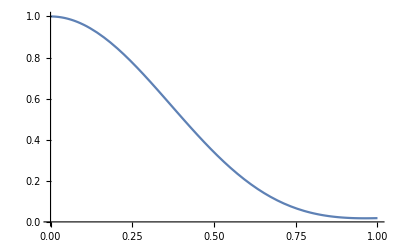

```mathematica
Plot[(Abs[(0.03191978647056788-0.0861342068674639 ⅈ) ((0.+0. ⅈ)+(0.03191978647056805+0.08613420686746417 ⅈ) (ⅇ^(2.220446049250313*^-16 t) Cos[0.506986828724842 t]-ⅈ ⅇ^(2.220446049250313*^-16 t) Sin[0.506986828724842 t]))+(0.18813396262556914-0.10764231494615971 ⅈ) ((0.+0. ⅈ)+(0.18813396262556933+0.10764231494615983 ⅈ) (ⅇ^(1.2802259252708836*^-15 t) Cos[1.568958264663573 t]-ⅈ ⅇ^(1.2802259252708836*^-15 t) Sin[1.568958264663573 t]))+(0.13485577490045986-0.31556347561695086 ⅈ) ((0.+0. ⅈ)+(0.13485577490046008+0.31556347561695103 ⅈ) (ⅇ^(8.686630969013966*^-16 t) Cos[2.763273009550849 t]-ⅈ ⅇ^(8.686630969013966*^-16 t) Sin[2.763273009550849 t]))+(0.20879595089836336-0.376443996327431 ⅈ) ((0.+0. ⅈ)+(0.20879595089836306+0.37644399632743086 ⅈ) (ⅇ^(-8.682294479477204*^-16 t) Cos[4.100559655348802 t]-ⅈ ⅇ^(-8.682294479477204*^-16 t) Sin[4.100559655348802 t]))-(0.35910746293649737-0.2883076444994744 ⅈ) ((0.+0. ⅈ)-(0.35910746293649765+0.2883076444994749 ⅈ) (ⅇ^(-4.445662576965769*^-15 t) Cos[5.485124198797293 t]-ⅈ ⅇ^(-4.445662576965769*^-15 t) Sin[5.485124198797293 t]))+(0.1270198778658047+0.4073017685670641 ⅈ) ((0.+0. ⅈ)+(0.12701987786580493-0.40730176856706424 ⅈ) (ⅇ^(8.154547240452292*^-17 t) Cos[6.752925682728906 t]-ⅈ ⅇ^(8.154547240452292*^-17 t) Sin[6.752925682728906 t]))-(0.17878409427525294+0.36021162986803607 ⅈ) ((0.+0. ⅈ)-(0.1787840942752518-0.3602116298680362 ⅈ) (ⅇ^(-2.411534833539539*^-15 t) Cos[7.86961596292701 t]-ⅈ ⅇ^(-2.411534833539539*^-15 t) Sin[7.86961596292701 t]))-(0.14510583208906586+0.2542212227571725 ⅈ) ((0.+0. ⅈ)-(0.14510583208906616-0.2542212227571715 ⅈ) (ⅇ^(3.564206221460181*^-15 t) Cos[8.202556397258723 t]-ⅈ ⅇ^(3.564206221460181*^-15 t) Sin[8.202556397258723 t]))])^2,{t,0,1},PlotRange->{0,1}]
```